```mathematica
Solve[b0==-c^2/(Phi1fp*R*OmegaF*(1-mufp/gam)*gam),gam]
```

{{gam→(-c^2+b0 mufp OmegaF Phi1fp R)/(b0 OmegaF Phi1fp R)}}

```mathematica
solsfuncth
```

{{}}

```mathematica
functh
```

True

```mathematica
Aphi[r,th]
```

0

```mathematica
Aphicoll[r,th]
```

(r/rfp)^nucoll (1-Cos[th]+0.0882353 Sin[th])

```mathematica
normaphi[r,th]
```

-(-2.-2. (rmono/rfp)^(2. nucoll))/(2 rfp^2 √(1.+(rmono/rfp)^(-2. nucoll)) (1.+(rmono/rfp)^(2. nucoll)))

```mathematica
Aphi[r,th]
```

-(2 Br0 rfp^2 √(1.+(rmono/rfp)^(-2. nucoll)) (1.+(rmono/rfp)^(2. nucoll)))/((-2.-2. (rmono/rfp)^(2. nucoll)) √((r/rfp)^(-2 nucoll)/(1-Cos[th]+0.0882353 Sin[th])^2+(rmono/rfp)^(-2 nucoll)/(1-Cos[th]+0.0882353 Sin[th])^2))

```mathematica
solsfuncth
```

{{}}

```mathematica
consts
```

consts

```mathematica
crapconsts={rfp->0.4*10^6,thfp->Pi/4,rmono->3*10^(10),nucoll->0,Br0->1,r->10^(10)};
```

```mathematica
myeq[r_,th_,theconsts_]:=(Aphi[rfp,thfp]==Aphi[r,th])//.crapconsts
```

```mathematica
FindRoot[myeq[r,th,theconsts],{th,Pi/4},WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function (5.684559897984485`*^10 == 2.9130966543697256`*^14/√1/(1 - « 1 » + 0.08823529411764706` « 1 »)^2) is less than WorkingPrecision (30.).

{th→0.00218452411445594782087643752844}

```mathematica
{th->0.00218452411445594782087643752844313799110012905`30.}
```

```mathematica
{th->0.017937339272515421968245118419289471182960021313`30.}
```

```mathematica
0.00218452411445594782087643752844313799110012905`30./0.017937339272515421968245118419289471182960021313`30.
```

0.12178640774237881800446095221

```mathematica
{th->0.00218452411445594782087643752844313799110012905`30.}
```

{th→0.00218452411445594782087643752844}

```mathematica
%[[1,2]]
```

0.00218452411445594782087643752844

```mathematica
Clear[functh]
```

3000000000000

FindRoot::precw: The precision of the argument function (82.37694970603116` == 1.5999999999999997`*^11 ((1 - ⅇ^99/100) (1 - Cos[th$154359]) + ⅇ^99/100 TagBox[« 1 », False, Rule[Editable, False]][th$154359])) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {-1.6592540017165431`*^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-4.107371627206345`*^-9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

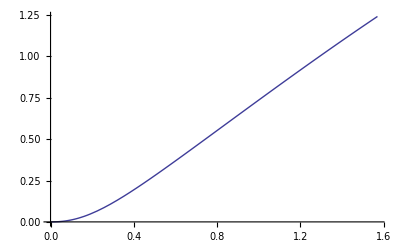

3000000000000

FindRoot::precw: The precision of the argument function (1.6`*^11 (« 32619 » (1 - Cos[thfp$157419]) + 2.22921387757731164962383945`11.079534297431001*^-32572 TagBox[InterpolatingFunction[{{0.`, 1.5707963267948966`}}, {3, 3, 0, {201}, {4}, 0, 0, 0, 0}, « 1 », {Developer`PackedArrayForm, {« 1 »}, {0.`, 0.00002463133756508912`, 0.000025731805442649007`, « 46 », 0.00020112196984399912`, « 151 »}}, {Automatic}], False, Rule[Editable, False]][« 11 »]) == « 22 ») is less than WorkingPrecision (30.).

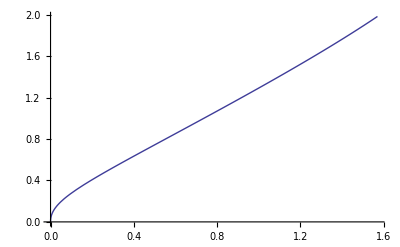

```mathematica
myr=10^2*rmono//.crapconsts
Plot[(thofr[myr,mythfp,crapconsts]//.crapconsts),{mythfp,0,Pi/2}]
myr=10^2*rmono//.crapconsts
Plot[(thfpofrth[myr,myth,crapconsts]//.crapconsts),{myth,0,Pi/2}]
```

```mathematica
Aphi[r,th]
```

1/(1+0.0882438 ⅇ^(1-rmono/rfp))Br0 (r/rfp)^((1-ⅇ^(1-rmono/r)) nucoll) rfp^2 ((1-ⅇ^(1-rmono/r)) (1-Cos[th])+ⅇ^(1-rmono/r) InterpolatingFunction[{{0.,1.5708}},<>][th])

```mathematica
crapconsts={rfp->0.4*10^6,thfp->Pi/2,rmono->3*10^(10),nucoll->3/4,Br0->1,Bphi0->1,tl->rfp/c,C0->3,c->3*10^(10),mueq->10^4,Br0gauss->Br0*Sqrt[4*Pi]};
myr=5*10^(13);
mythfp=thfp//.crapconsts
myth=thofr[myr,mythfp,crapconsts]
Brnearly[r,th]//.crapconsts//.{r->rmono,th->0.01}//.crapconsts
Bhnearly[r,th]//.crapconsts//.{r->rmono,th->0.01}//.crapconsts
Bpnearly[r,th]//.crapconsts//.{r->rmono,th->0.01}//.crapconsts
Bphistart[r,th]//.crapconsts//.{r->rmono,th->0.01}//.crapconsts
omegaf[r,th,crapconsts]//.crapconsts//.{r->rmono,th->0.01}//.crapconsts
omegaffp[r,th,crapconsts]//.crapconsts//.{r->rmono,th->0.01}//.crapconsts
Rfp[myr,myth,crapconsts]//.crapconsts
(thfpofrth[myr,myth,crapconsts])
gamma1dep[myr,myth,crapconsts]//.crapconsts
gamma1[myr,myth,crapconsts]//.crapconsts
gamma2[myr,myth,crapconsts]//.crapconsts
Print["mygammaff"];
mygammaff[myr,myth,crapconsts]//.crapconsts
Print["mysemigammacoll"];
mysemigammacoll[myr,myth,crapconsts]//.crapconsts
gammafp[myr,myth,crapconsts]//.crapconsts
Print["mufp"];
mufp[myr,myth,crapconsts]//.crapconsts
mygamma0[myr,myth,crapconsts]//.crapconsts
Print["mygammacoll"];
mygammacoll[myr,myth,crapconsts]//.crapconsts
```

π/2

FindRoot::precw: The precision of the argument function (1.6`*^11 == 7.25130095365624`*^14 ((1 - 1/ⅇ^3/5000) (1 - Cos[th$114956]) + TagBox[InterpolatingFunction[{{0.`, 1.5707963267948966`}}, « 3 », {Automatic}], False, Rule[Editable, False]][th$114956]/ⅇ^3/5000)) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {1.57079632679489661923132169163975144209858327474`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.001140201606574793292341839095

Brnearly[30000000000,0.01]

Bhnearly[30000000000,0.01]

Bpnearly[30000000000,0.01]

Bphistart[30000000000,0.01]

18750.

18750.

FindRoot::precw: The precision of the argument function (1.6`*^11 (« 32618 » (1 - Cos[thfp$114980]) + 8.2008195553476544645121993`11.079528506799303*^-32573 TagBox[InterpolatingFunction[{{0.`, 1.5707963267948966`}}, {3, 3, 0, {201}, {4}, 0, 0, 0, 0}, « 1 », {Developer`PackedArrayForm, {« 1 »}, {0.`, 0.00002463133756508912`, 0.000025731805442649007`, « 46 », 0.00020112196984399912`, « 151 »}}, {Automatic}], False, Rule[Editable, False]][« 11 »]) == « 8 ») is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {10.01254221767232272621576023004502130183`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {11.51331712132555483103585108322045161134`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

-400000.

10.9955742875642763346192518415

35631.3

√Max[1,1.26959×10^9+gamma0^2]

2.14829529151562375072163133872×10^18

mygammaff

(2000000000000000000000000000000 √(3/1999999999999999999999999999999) √Max[1,1.26959×10^9+gamma0^2])/(√(12000000000000000000000000000000000000000000000000000000000000/1999999999999999999999999999999+1.3000597036357397064227722032×10^-6 Max[1,1.26959×10^9+gamma0^2]))

mysemigammacoll

InterpolatingFunction::dmval: Input value {10.99557428756427633461925184147826009469`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

1/(0.000230879+(√(1999999999999999999999999999999/3) √(12000000000000000000000000000000000000000000000000000000000000/1999999999999999999999999999999+1.3000597036357397064227722032×10^-6 Max[1,1.26959×10^9+gamma0^2]))/(2000000000000000000000000000000 √Max[1,1.26959×10^9+gamma0^2]))

InterpolatingFunction::dmval: Input value {10.99557428756427633461925184147826009469`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

1.1547

mufp

InterpolatingFunction::dmval: Input value {10.99557428756427633461925184147826009469`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

4331.28

InterpolatingFunction::dmval: Input value {10.99557428756427633461925184147826009469`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::precw: The precision of the argument function (1.6`*^11 (« 32618 » (1 - Cos[thfp$115077]) + 8.2008195553476544645121993`11.079528506799303*^-32573 TagBox[InterpolatingFunction[{{0.`, 1.5707963267948966`}}, {3, 3, 0, {201}, {4}, 0, 0, 0, 0}, « 1 », {Developer`PackedArrayForm, {« 1 »}, {0.`, 0.00002463133756508912`, 0.000025731805442649007`, « 46 », 0.00020112196984399912`, « 151 »}}, {Automatic}], False, Rule[Editable, False]][« 11 »]) == « 8 ») is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {10.99557428756427633461925184147826009469`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

1

mygammacoll

InterpolatingFunction::dmval: Input value {10.99557428756427633461925184147826009469`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

3861.84

```mathematica
Phi1fp[myr,myth,crapconsts]//.crapconsts
Bphifp[myr,myth,crapconsts]//.crapconsts
mufp[myr,myth,crapconsts]//.crapconsts
```

1.03923×10^15

-1.94868×10^-7

1.1547

```mathematica
myr
myth
```

50000000000000

0.02

```mathematica
myrfp=rfp//.crapconsts
mythfp=(thfpofrth[myr,myth,crapconsts])
Phi1fp[myrfp,mythfp,crapconsts]//.crapconsts
Bphifp[myrfp,mythfp,crapconsts]//.crapconsts
mufp[myrfp,mythfp,crapconsts]//.crapconsts
```

400000.

7.79472744785078131173488131167×10^-7

1.03923×10^15

-1.94868×10^-7

1.1547

```mathematica
Plot[thfpofrth[5*10^(9),th,crapconsts],{th,0,Pi/2}]
```

FindRoot::precw: The precision of the argument function (1.6`*^11 (« 32619 » (1 - Cos[thfp$12145]) + 2.22921387757731164962383945`11.079534297431001*^-32572 TagBox[InterpolatingFunction[{{0.`, 1.5707963267948966`}}, {3, 3, 0, {201}, {4}, 0, 0, 0, 0}, « 1 », {Developer`PackedArrayForm, {« 1 »}, {0.`, 0.00002463133756508912`, 0.000025731805442649007`, « 46 », 0.00020112196984399912`, « 151 »}}, {Automatic}], False, Rule[Editable, False]][« 10 »]) == « 22 ») is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {2.0579959808973287`} lies outside the range of data in the interpolating function. Extrapolation will be used.

$Aborted

```mathematica
Aphi[10^6,0.02,crapconsts]//.crapconsts
```

FindRoot::precw: The precision of the argument function (1 == 4532.063096035153` (1 - Cos[th$323709])) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (1 == 4532.063096035153` (1 - Cos[th$323763])) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (1 == 4532.063096035153` (1 - Cos[th$323817])) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot will be suppressed during this calculation.

6.36195×10^7

```mathematica
Bprsq[0.02,crapconsts]
```

FindRoot::precw: The precision of the argument function (1 == 4532.063096035153` (1 - Cos[th$629077])) is less than WorkingPrecision (30.).

1.34332

```mathematica
Aphi[10^6,0.02,crapconsts]
```

FindRoot::precw: The precision of the argument function (1 == 4532.063096035153` (1 - Cos[th$649972])) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (1 == 4532.063096035153` (1 - Cos[th$650026])) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (1 == 4532.063096035153` (1 - Cos[th$650080])) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot will be suppressed during this calculation.

(3.18108×10^11 Br0 (0.00186335 ⅇ^(-rmono/1000000)+0.000199993 (1-ⅇ^(-rmono/1000000))))/(1-6.0929 ⅇ^(-2.5×10^-6 rmono))

```mathematica
myrfp=rfp//.crapconsts
myr=10^8;
functh[rvar_?NumericQ,th_?NumericQ,theconstsvar_]:=(Aphi[myrfp,Pi/2]==Aphi[rvar,th])//.crapconsts;
rootsol=FindRoot[functh[myr,th,crapconsts],{th,Pi/2},WorkingPrecision->30];
```

400000.

ReplaceRepeated::reps: {π/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$829951] (1 + 0.08823529411764706` (1/Sin[th$829951]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {π/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$829951] (1 + 0.08823529411764706` (1/Sin[th$829951]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {π/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated will be suppressed during this calculation.

NIntegrate::inumr: The integrand Sin[th$829951] (1 + 0.08823529411764706` (1/Sin[th$829951]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

$Aborted

```mathematica
myrfp=rfp//.crapconsts;
myr=10^6;
mythfp=Pi/2;
theconsts=crapconsts;
functh[rvar_?NumericQ,th_?NumericQ,theconstsvar_]:=(Aphi[myrfp,mythfp,theconsts]-Aphi[rvar,th,theconsts])//.theconstsvar;
rootsol=FindRoot[0==functh[myr,th,theconsts],{th,mythfp},WorkingPrecision->30];
```

ReplaceRepeated::reps: {π/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$1515184] (1 + 0.08823529411764706` (1/Sin[th$1515184]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {π/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$1515184] (1 + 0.08823529411764706` (1/Sin[th$1515184]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {π/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated will be suppressed during this calculation.

NIntegrate::inumr: The integrand Sin[th$1515184] (1 + 0.08823529411764706` (1/Sin[th$1515184]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

$Aborted

```mathematica
Bprsq[0.01,crapconsts]
```

FindRoot::precw: The precision of the argument function (1.0000000000000002` == 4532.063096035153` (1 - Cos[th$1515173])) is less than WorkingPrecision (30.).

8.80352

```mathematica
thofr[10^6,Pi/2,crapconsts]
```

$Aborted

```mathematica
thfpofrth[10^6,0.1,crapconsts]
thfpofrth[1*10^(10),0.02,crapconsts]
thfpofrth[4*10^(10),0.01,crapconsts]
thfpofrth[5*10^(13),0.01,crapconsts]
```

ReplaceRepeated::reps: {thfp$670785} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$670786] (1 + 0.08823529411764706` (1/Sin[th$670786]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {thfp$670785} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$670786] (1 + 0.08823529411764706` (1/Sin[th$670786]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {thfp$670785} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated will be suppressed during this calculation.

NIntegrate::inumr: The integrand Sin[th$670786] (1 + 0.08823529411764706` (1/Sin[th$670786]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

$Aborted

ReplaceRepeated::reps: {thfp$777289} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$777290] (1 + 0.08823529411764706` (1/Sin[th$777290]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {thfp$777289} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

ReplaceRepeated::reps: {thfp$777353} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$777354] (1 + 0.08823529411764706` (1/Sin[th$777354]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {thfp$777353} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$777354] (1 + 0.08823529411764706` (1/Sin[th$777354]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {thfp$777353} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated will be suppressed during this calculation.

NIntegrate::inumr: The integrand Sin[th$777354] (1 + 0.08823529411764706` (1/Sin[th$777354]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

$Aborted

ReplaceRepeated::reps: {thfp$779895} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$779896] (1 + 0.08823529411764706` (1/Sin[th$779896]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {thfp$779895} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand Sin[th$779896] (1 + 0.08823529411764706` (1/Sin[th$779896]^1.1` - 1/Sin[thofrpre[« 3 »]]^1.1`)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1/10000}}.

ReplaceRepeated::reps: {thfp$779895} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated will be suppressed during this calculation.

$Aborted

```mathematica
thofrpre[10^6,0.1,crapconsts]
```

FindRoot::precw: The precision of the argument function (0.0049958347219741794` == 1.9881768219176272` (1 - Cos[th$273524])) is less than WorkingPrecision (30.).

0.0709059218710830517547343300156

```mathematica
Bprsq[0.1,crapconsts]
```

FindRoot::precw: The precision of the argument function (1 == 4532.063096035153` (1 - Cos[th$273536])) is less than WorkingPrecision (30.).

-4.06823

```mathematica
Aphicollgen[10^6,0.1,3/4
```

```mathematica
toplot=Aphi[r,th]//.crapconsts//.{r->10^lr};
```

```mathematica
thofr[10^6,Pi/2]
```

thofr[1000000,π/2]

FindRoot::precw: The precision of the argument function (1.6`*^11 == 1.3426931549037813`*^11 (« 41191 » (1 - Cos[th$121747]) + 9.97344830864116616906`10.813304385880164*^-41151 TagBox[« 1 », False, Rule[Editable, False]][th$121747])) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {1.57079632679489661923132169163975144209858327474`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.76243120938626395400672501138458603060164164057`30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (4.68629150101524`*^10 == 1.3426931549037813`*^11 (« 41191 » (1 - Cos[th$121792]) + 9.97344830864116616906`10.813304385880164*^-41151 TagBox[InterpolatingFunction[{{0.`, 1.5707963267948966`}}, {3, 3, 0, {201}, {4}, 0, 0, 0, 0}, « 1 », {Developer`PackedArrayForm, {« 1 »}, {0.`, 4.99999999583334`*^-9, « 47 », 5.287237281921684`*^-7, « 151 »}}, {Automatic}], False, Rule[Editable, False]][« 9 »])) is less than WorkingPrecision (30.).

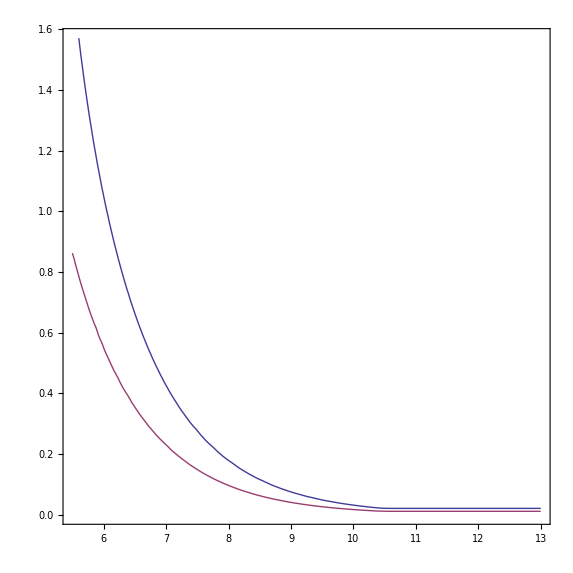

```mathematica
ContourPlot[{thofr[10^lr,Pi/2,crapconsts]==th,thofr[10^lr,Pi/4,crapconsts]==th},{lr,5.5,13},{th,0,Pi/2}]
```

```mathematica
myrmono=rmono//.crapconsts
thmono=thofr[myrmono,Pi/2,crapconsts]
```

30000000000

0.021007530849255049652156682215

```mathematica
0.85+0.075*(Sin[th]/Sin[thmono])^(-1.1)//.{th->0.021}
0.85+0.075*(Sin[th]/Sin[thmono])^(-1.1)//.{th->0.01}
0.85+0.075*(Sin[th]/Sin[thmono])^(-1.1)//.{th->0.001}
```

0.92503

1.01969

2.98618

```mathematica
1+0.075/0.85*(Sin[th]^(-1.1)-Sin[thmono]^(-1.1))//.{th->0.021}
1+0.075/0.85*(Sin[th]^(-1.1)-Sin[thmono]^(-1.1))//.{th->0.01}
1+0.075/0.85*(Sin[th]^(-1.1)-Sin[thmono]^(-1.1))//.{th->0.001}
1+0.075/0.85*(Sin[th]^(-1.1)-Sin[thmono]^(-1.1))//.{th->0.0001}
```

1.00244

8.80352

170.872

2211.19

```mathematica
aphisimplemono[th_]:=1-Cos[th];
Aphicollpre[r_,th_,mynu_]:=(r/rfp)^mynu*aphisimplemono[th];
ClearAll[thofrpre];
thofrpre[r_?NumericQ,thfp_?NumericQ,theconsts_]:=Module[{result,th,rvar,theconstsvar,functh,rootsol},
functh[rvar_,th_,theconstsvar_]:=(Aphicollpre[rfp,thfp,nucoll]==Aphicollpre[rvar,th,nucoll])//.theconstsvar;
rootsol=FindRoot[functh[r,th,theconsts],{th,thfp},WorkingPrecision->30];
result=rootsol[[1,2]];
(* return *)
result
];
```

```mathematica
thofrpre[myrmono,Pi/2,crapconsts]
```

FindRoot::precw: The precision of the argument function (1 == 4532.063096035153` (1 - Cos[th$124634])) is less than WorkingPrecision (30.).

0.0210075308494614202217427625457

```mathematica
Clear[normaphi]
```

3/4 (1-ⅇ^(-3 10^(10-lr)))

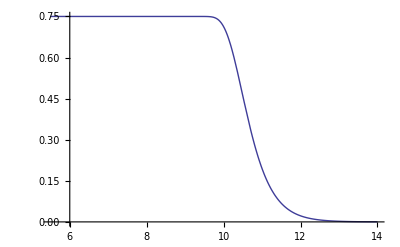

```mathematica
toplot=thenufunc[r]//.{r->10^lr}//.crapconsts
Plot[toplot,{lr,5.5,14}]
```

```mathematica
rfp
```

rfp

(2.9131×10^-6 Csc[th] (0.0882353 Cos[th]+Sin[th]))/((1/(1-Cos[th]+0.0882353 Sin[th])^2)^(3/2) (1-Cos[th]+0.0882353 Sin[th])^3)

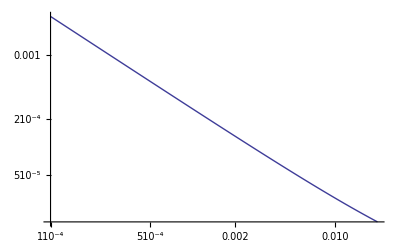

```mathematica
toplot=(D[Aphi[r,th],th]/(r^2*Sin[th]))//.crapconsts
LogLogPlot[toplot,{th,10^(-4),0.02}]
```

```mathematica
Clear[Bprsq]
```

```mathematica
Limit[toplot,th->0]
```

∞

```mathematica
Integrate[1*Sin[th],{th,0,thp}]
```

1-Cos[thp]

```mathematica
toplot//.{th->0.002}
```

2.9131×10^-6

```mathematica
Solve[it,th]
```

Hold[Abort[],Abort[]]

```mathematica
faphi[0.02]
```

0.00309952

```mathematica
ifaphi[0.021]
```

0.00325018

```mathematica
D[ifaphi[x],x]
```

InterpolatingFunction[{{0.0001,1.5708}},<>][x]

```mathematica
(D[Aphicoll[r,th],th]/(rfp^2*Sin[th]))//.{r->rfp}//.crapconsts//.{th->Pi/2}
(D[Aphicoll[r,th],th]/(rfp^2*Sin[th]))//.{r->rfp}//.crapconsts//.{th->0.00001}
```

6.25×10^-12

6.25×10^-12

```mathematica
(D[Aphicoll[r,th],th]/(rfp^2*Sin[th]))//.{r->rmono/2}//.crapconsts//.{th->Pi/2}
(D[Aphicoll[r,th],th]/(rfp^2*Sin[th]))//.{r->rmono/2}//.crapconsts//.{th->0.00001}
```

6.45289×10^-12

6.29212×10^-8

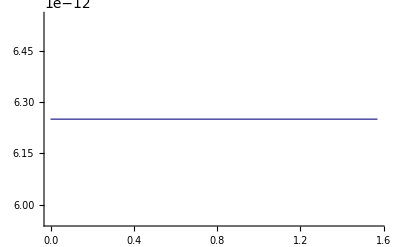

```mathematica
toplot=Brtemp[rfp,th]//.crapconsts;
Plot[toplot,{th,0,Pi/2}]
```

```mathematica
crapconsts={rfp->0.4*10^6,thfp->Pi/4,rmono->3*10^(10),nucoll->0,Br0->1};
myth=0.000001;
ifaphi[myth]//.crapconsts
Exp[-rmono/rfp]/Exp[-1]//.crapconsts
aphimono[myth]//.crapconsts
N[(1-Exp[-rmono/rfp]/Exp[-1])//.crapconsts,13]
```

2.82585×10^-7

2.2292138776×10^-32572

5.00044×10^-13

1.

```mathematica
finalaphith[rfp,0.000001]//.crapconsts
```

5.00044×10^-13

```mathematica
Exp[-rmono/rfp]//.crapconsts
```

8.2008195553×10^-32573

```mathematica
faphitable
```

```mathematica
Clear[ifaphi,faphitable0,faphitable]
```